# PlotFunctions

## Tyson Jones tyson.jones@monash.edu August 2017

## Package Test

```mathematica
Clear["Global`*"]
```

## Import

The location of the folder containing the package must be added to the paclet directories

In rare circumstances, the PacletManager` context will not be known, and must be prepended to the below call

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
<< WavefunctionSolver`
```

## One Dimension

```mathematica
Options[PlotWavefunction]
```

{Potential→None,PotentialTransform→(#1&),PotentialPlotOptions→{},ShowBar→True,ColorScheme→Rainbow}

## Functions

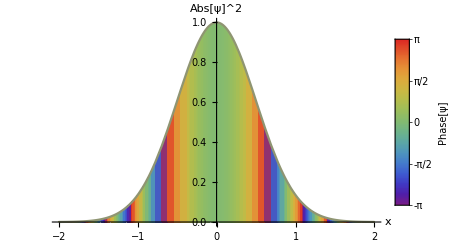

```mathematica
PlotWavefunction[
	Exp[8ⅈ#^2-#^2]&,
	{-2, 2}
]
```

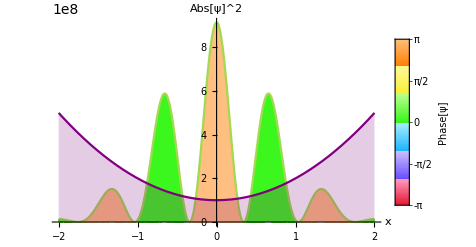

```mathematica
PlotWavefunction[
	Function[{x},Exp[-x^2]HermiteH[10, x]],
	{uselessvar, -2, 2},
	ColorScheme -> "BrightBands",
	Potential ->  (#^2&),
	PotentialTransform  -> (10^8 # + 10^8&),
	PotentialPlotOptions -> {PlotStyle -> Purple},
	LabelStyle -> Blue
]
```

InterpolatingFunction[{{0, 1}}, <>]

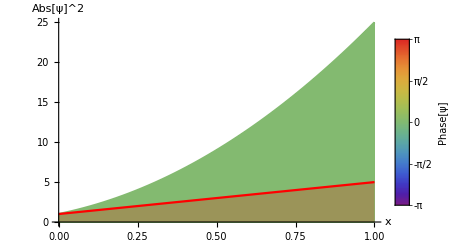

```mathematica
ListInterpolation[{1, 2, 3, 4, 5}, {{0, 1}}]
PlotWavefunction[%, {0, 1}, Potential -> %]
```

## Lists

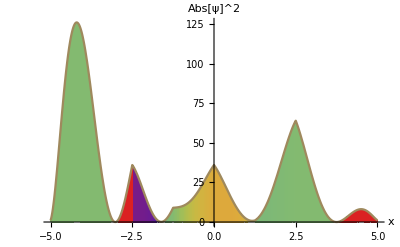

```mathematica
PlotWavefunction[
	{1, 9, 6 ⅇ^(-π ⅈ), 3, 6 ⅈ, 1, 8, 0, -1},
	{-5, 5},
	ShowBar -> False
]
```

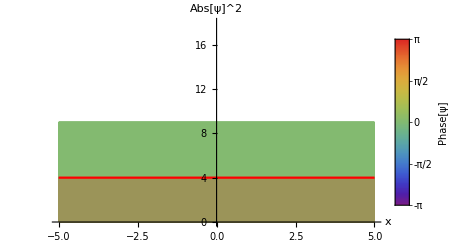

```mathematica
PlotWavefunction[
	{3, 3, 3, 3, 3},
	{-5, 5},
	Potential -> {2, 2, 2, 2, 2},
	PotentialTransform -> (2 #&)
]
```

## Quantities

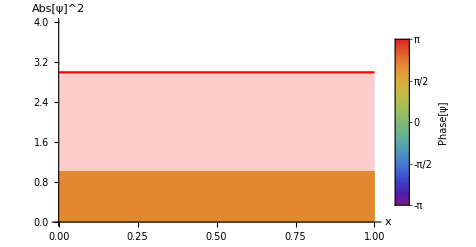

```mathematica
PlotWavefunction[
	ⅈ,
	{0, 1},
	Potential -> 3,
	PlotRange -> {0, 4}
]
```

## Symbolic Expressions

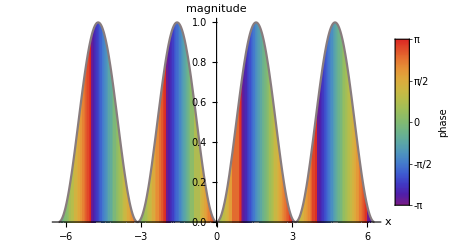

```mathematica
PlotWavefunction[
	Sin[x] Exp[x π ⅈ],
	{x, -2 π, 2 π},
	AxesLabel -> {"x", "magnitude"},
	LegendLabel -> "phase"
]
```

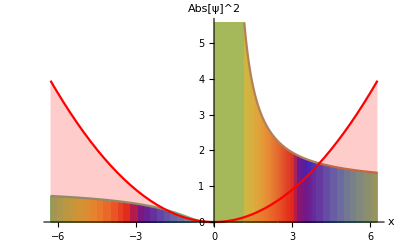

```mathematica
PlotWavefunction[
	Exp[1/s +s ⅈ],
	{s, -2 π, 2 π},
	Potential -> s^2/10,
	LegendFunction -> "Frame"
]
```

## Mixed

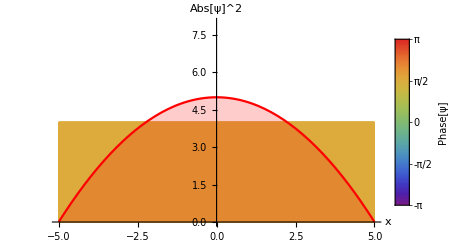

```mathematica
PlotWavefunction[
	2 ⅈ,
	{x, -5, 5},
	Potential -> -x^2/5 + 5
]
```

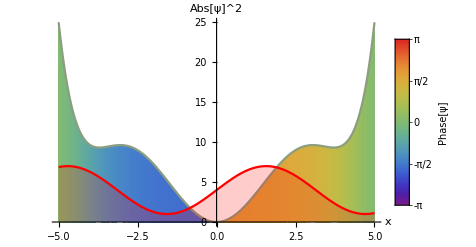

```mathematica
PlotWavefunction[
	{5, -3ⅈ, 0, 3ⅈ, 5},
	{z, -5, 5},
	Potential -> Sin[z],
	PotentialTransform -> Function[V, 3 V + 4]
]
```

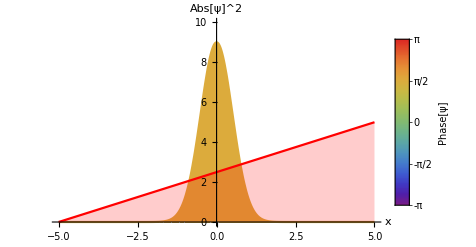

```mathematica
PlotWavefunction[
	3 Exp[-x^2] ⅈ,
	{x, -5, 5},
	Potential -> {0, 1, 2, 3, 4,5},
	PlotRange -> {0, 10}
]
```

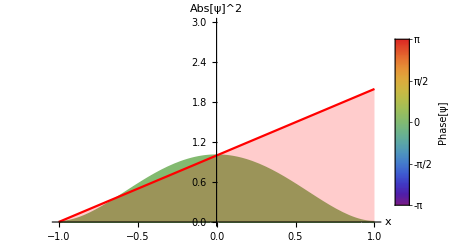

```mathematica
PlotWavefunction[
	Function[{x}, - x^2+1],
	{s, -1, 1},
	Potential -> s + 1,
	PlotRange -> {0, 3}
]
```

## Non - matching

The wavefunction is symbolic, but the symbol x has not been passed

```mathematica
PlotWavefunction[
	Exp[-x^2] HermiteH[3, x],
	{-3, 3}
]
```

PlotWavefunction[ⅇ^(-x^2) (-12 x+8 x^3),{-3,3}]

Potential is symbolic, but the symbol x has not been passed

```mathematica
PlotWavefunction[
	5,
	{-3, 3},
	Potential -> x^2
]
```

PlotWavefunction[5,{-3,3},Potential→x^2]

The wavefunction is a 2D pure function, but only a single domain has been passed

```mathematica
PlotWavefunction[
	(#2&),
	{-3, 3}
]
```

PlotWavefunction[#2&,{-3,3}]

The wavefunction is a 2D function, but only a single domain has been passed

```mathematica
PlotWavefunction[
	Function[{x, y}, Exp[- x y]],
	{-3, 3}
]
```

PlotWavefunction[Function[{x,y},Exp[-x y]],{-3,3}]

The wavefunction is a (2D) matrix, but only a single domain has been passed

```mathematica
PlotWavefunction[
	({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}),
	{-3, 3}
]
```

PlotWavefunction[{{1,2,3},{4,5,6},{7,8,9}},{-3,3}]

Potential is a 2D pure function, but only a single domain has been passed

```mathematica
PlotWavefunction[
	Function[x, x^2],
	{-3, 3},
	Potential -> (#2&)
]
```

PlotWavefunction[Function[x,x^2],{-3,3},Potential→(#2&)]

Potential is a 2D function, but only a single domain has been passed

```mathematica
PlotWavefunction[
	Function[x, x^2],
	{-3, 3},
	Potential -> Function[{x, y}, x+y]
]
```

PlotWavefunction[Function[x,x^2],{-3,3},Potential→Function[{x,y},x+y]]

Potential is a (2D) matrix, but only a single domain has been passed

```mathematica
PlotWavefunction[
	Function[x, x^2],
	{-3, 3},
	Potential -> ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})
]
```

PlotWavefunction[Function[x,x^2],{-3,3},Potential→{{1,2,3},{4,5,6},{7,8,9}}]

PotentialTransform is not a 1D function

```mathematica
PlotWavefunction[
	Function[x, x^2],
	{-3, 3},
	Potential -> 5,
	PotentialTransform -> (#2&)
]
```

PlotWavefunction[Function[x,x^2],{-3,3},Potential→5,PotentialTransform→(#2&)]

The passed domain is non-numeric (containing an unknown symbol p)

```mathematica
PlotWavefunction[
	x^2,
	{x, p, 2p}
]
PlotWavefunction[
	#^2&,
	{p, 2p}
]
```

PlotWavefunction[x^2,{x,p,2 p}]

PlotWavefunction[#1^2&,{p,2 p}]

The passed domain is non-real

```mathematica
PlotWavefunction[
	x^2,
	{x, 0, ⅈ}
]
```

PlotWavefunction[x^2,{x,0,ⅈ}]

The passed wavefunction vector is non-numeric (containing symbol Graph)

```mathematica
PlotWavefunction[
	{1, 2, Graph, 4, 5},
	{-3, 3}
]
```

PlotWavefunction[{1,2,Graph,4,5},{-3,3}]

(though the above would still match - and fail to render - if a symbol was passed in the domain)

The passed wavefunction quantity is non-numeric

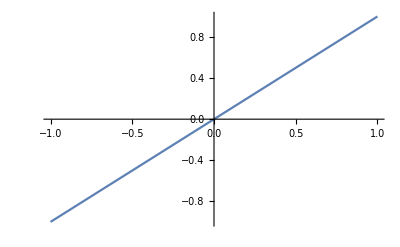
PlotWavefunction[-Graphics-,{-3,3}]

```mathematica
PlotWavefunction[
	Plot[x, {x, -1, 1}],
	{-3, 3}
]
```

(though the above would still match - and fail to render - if a symbol was passed in the domain)

Two domains (2D) are passed, yet an incompatible (1D) vector is passed

```mathematica
PlotWavefunction[
	 {1, 2, 3, 4, 5}, 
	{0, 1},
	{0, 1}
]
```

PlotWavefunction[{1,2,3,4,5},{0,1},{0,1}]

## Matching but unable to render correctly

The wavefunction contains an unknown symbol y, so isn’t shown

```mathematica
PlotWavefunction[
	y^2,
	{x, -5, 5}
]
```

-Graphics-

Potential contains an unknown symbol y, so isn’t shown

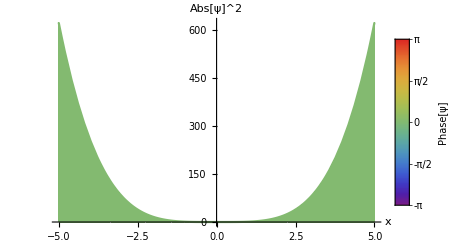

```mathematica
PlotWavefunction[
	x^2,
	{x, -5, 5},
	Potential -> y^2
]
```

PotentialTransform contains an unknown symbol, so the Potential isn’t shown

```mathematica
PlotWavefunction[
	x^2,
	{x, -5, 5},
	Potential ->10 x^2,
	PotentialTransform -> (cons #&)
]
```

-Graphics-

Potential isn’t real

```mathematica
PlotWavefunction[
	x^2,
	{x, -5, 5},
	Potential -> ⅈ x
]
```

-Graphics-

When a symbol is present in the domain, any wavefunction type will match...

```mathematica
PlotWavefunction[
	Plot[x, {x, -1, 1}],
	{a, -3, 3}
]
```

-Graphics-

... and will render if the underlying Plot function can render the type. The ColorFunction will not render for lists, for example

```mathematica
PlotWavefunction[
	{ⅈ x, x^2, x^3},
	{x, -5, 5}
]
```

-Graphics-

## Matching with superfluous arguments

The wavefunction and potential are passed as a functions, so the passed symbol z is unnecessary and irrelevant

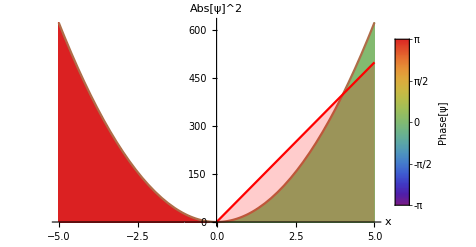

```mathematica
PlotWavefunction[
	Function[{x}, 5x],
	{z, -5, 5},
	Potential -> (10^2 #&)
]
```

A Potential isn’t passed, so PotentialTransform is irrelevant

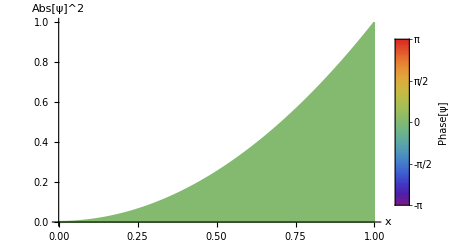

```mathematica
PlotWavefunction[x, {x, 0, 1}, PotentialTransform -> (#&)]
```

The colorbar isn’t shown (since ShowBar -> False), so the LegendLabel is irrelevant

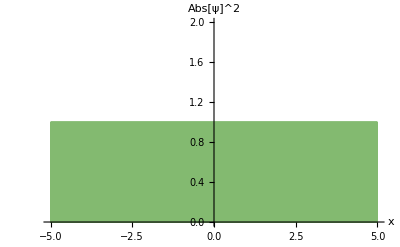

```mathematica
PlotWavefunction[
	1,
	{ -5, 5},
	ShowBar -> False,
	LegendLabel -> "a useless label"
]
```

## Throwing errors

Passing vectors causes interpolation. Too few entries will result in poor interpolation and a warning message

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2}.

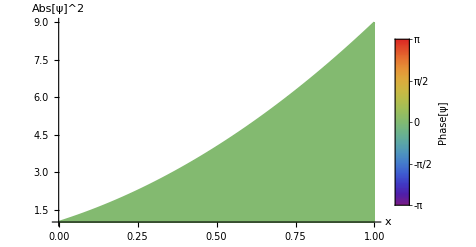

```mathematica
PlotWavefunction[
	 {1, 2, 3}, 
	{0, 1}
]
```

Attempting to pass non-accepted options will cause an error message, but not hinder rendering

OptionValue::nodef: Unknown option banana for {PlotWavefunction,WavefunctionSolver`PlotFunctions`PackagePrivate`plot1DWavefunction,BarLegend,Plot}.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

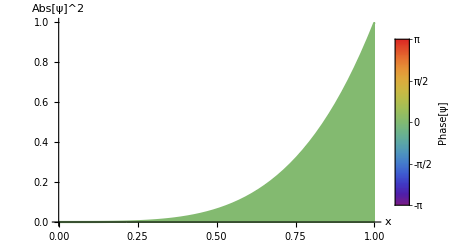

```mathematica
PlotWavefunction[
	x^2, 
	{x, 0, 1},
	banana -> poo
]
```

```mathematica
PlotWavefunction[
	x^2, 
	{x, 0, 1},
	MaxSteps -> 5
]
```

OptionValue::nodef: Unknown option MaxSteps for {PlotWavefunction,WavefunctionSolver`PlotFunctions`PackagePrivate`plot1DWavefunction,BarLegend,Plot}.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

-Graphics-

This is also true for non-Plot options in PotentialPlotOptions

OptionValue::nodef: Unknown option MaxSteps for Plot.

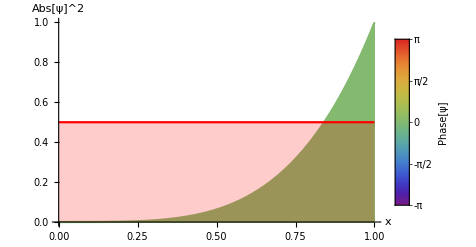

```mathematica
PlotWavefunction[
	x^2, 
	{x, 0, 1},
	Potential -> .5,
	PotentialPlotOptions -> {MaxSteps -> 3}
]
```

PlotWavefunction will accept Options[PlotWavefunction] and any options of Plot/Plot3D (depending on whether your wavefunction is 1D or 2D) and BarLegend

```mathematica
Options[PlotWavefunction]
Options[BarLegend]
Options[Plot]
Options[Plot3D]
```

{Potential→None,PotentialTransform→(#1&),PotentialPlotOptions→{},ShowBar→True,ColorScheme→Rainbow}

{LabelStyle→Automatic,LegendFunction→None,LegendLabel→None,LegendLayout→Automatic,LegendMargins→Automatic,LegendMarkers→None,LegendMarkerSize→Automatic,Method→None}

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClippingStyle→Automatic,ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Opacity[0.5],FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,ScalingFunctions→None,SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

## Two Dimensions

## Functions

```mathematica
PlotWavefunction[
	Exp[-#1^2-#2^2-#1 π ⅈ]&,
	{-1, 1},
	{-2, 2}
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	Function[{x, y},Exp[-x^2-y^2]HermiteH[1, x]HermiteH[1, y]],
	{-3, 3},
	{-3, 3},
	PlotRange -> {0, 1},
	ColorScheme -> "BrightBands",
	Potential ->  Function[{x, y}, x^2+y^2],
	PotentialTransform -> (#/9&),
	LabelStyle -> Blue
]
```

-Graphics3D-

```mathematica
ListInterpolation[({{1, 2, 3, 4, 5}, {6, 7 ⅇ^(-(ⅈ π)/3), 8, 9, 8}, {7, 6, 5ⅈ, 4, 3}, {2, 1, 2, ⅇ^ⅈ, 4}, {5 ⅇ^(-(ⅈ π)/3), 6, 7, 8, 9}}), {{0, 1}, {0, 1}}]
PlotWavefunction[%, {0, 1}, {0, 1}]
```

InterpolatingFunction[{{0, 1}, {0, 1}}, <>]

-Graphics3D-

## Matrices

```mathematica
PlotWavefunction[
	({{1, 2, 3, 4, 5}, {6, 7 ⅇ^(-(ⅈ π)/3), 8, 9, 8}, {7, 6, 5ⅈ, 4, 3}, {2, 1, 2, ⅇ^ⅈ, 4}, {5 ⅇ^(-(ⅈ π)/3), 6, 7, 8, 9}})^2,
	{-5, 5},
	{-4, 4},
	ShowBar -> False
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	Table[3, {i, 5}, {j, 5}],
	{-3, 3},
	{-2, 2},
	Potential ->Table[2, {i, 5}, {j, 5}]
]
```

-Graphics3D-

## Quantities

```mathematica
PlotWavefunction[
	ⅈ,
	{0, 1},
	{0, 1},
	Potential -> 3,
	PlotRange -> {0, 4}
]
```

-Graphics3D-

## Symbolic Expressions

```mathematica
PlotWavefunction[
	Sin[x]Cos[y] Exp[y x π ⅈ / 10],
	{x, -2 π, 2 π},
	{y, -2 π, 2 π},
	AxesLabel -> {"x", "y", "magnitude"},
	LegendLabel -> "phase",
	ImageSize -> Large
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	Exp[1/s +s ⅈ],
	{s, -2 π, 2 π},
	{t, 0, 10},
	Potential -> s^2/10,
	LegendFunction -> "Frame"
]
```

-Graphics3D-

## Mixed

```mathematica
PlotWavefunction[
	2 ⅈ,
	{x, -5, 5},
	{y, 0, 1},
	Potential -> -x^3 /5 + 5
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	Table[{5, -3ⅈ, 0, 3ⅈ, 5}, 5],
	{z, -5, 5},
	{w, 0, 1},
	Potential -> Sin[z],
	PotentialTransform -> Function[V, 5 V + 4]
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	3 Exp[-x^2] ⅈ Exp[- y^2],
	{x, -5, 5},
	{y, -5, 5},
	Potential -> 1({{1, 2, 3, 4, 5}, {6, 7, 8, 9, 8}, {7, 6, 5, 4, 3}, {2, 1, 2, 3, 4}, {5ⅇ, 6, 7, 8, 9}}),
	PlotRange -> {0, 10}
]
```

-Graphics3D-

```mathematica
PlotWavefunction[
	Function[{x, y}, - x^2+1],
	{s, -1, 1},
	{t, 0, 1},
	Potential -> s + 1,
	PlotRange -> {0, 3}
]
```

-Graphics3D-

## Non - matching

The wavefunction is symbolic, but the symbol x has not been passed

```mathematica
PlotWavefunction[
	Exp[-x^2] HermiteH[3, x],
	{ -3, 3},
	{ -3, 3}
]
```

PlotWavefunction[ⅇ^(-x^2) (-12 x+8 x^3),{-3,3},{-3,3}]

The wavefunction is symbolic, but only one of the two domains pass symbols

```mathematica
PlotWavefunction[
	Exp[-x^2] HermiteH[3, x],
	{x,  -3, 3},
	{ -3, 3}       (* should pass a dummy var here, like 'y' *)
]
```

PlotWavefunction[ⅇ^(-x^2) (-12 x+8 x^3),{x,-3,3},{-3,3}]

Potential is symbolic, but the symbol x has not been passed

```mathematica
PlotWavefunction[
	5,
	{-3, 3},
	{0, 1},
	Potential -> x^2
]
```

PlotWavefunction[5,{-3,3},{0,1},Potential→x^2]

The wavefunction is a 3D pure function; it must be at-most 2D

```mathematica
PlotWavefunction[
	(#3&),
	{ -3, 3},
	{ -2, 2}
]
```

PlotWavefunction[#3&,{-3,3},{-2,2}]

The wavefunction is a 3D pure function; it must be at-most 2D

```mathematica
PlotWavefunction[
	Function[{x, y, z},z Exp[- x y]],
	{-3, 3},
	{-2, 2}
]
```

PlotWavefunction[Function[{x,y,z},z Exp[-x y]],{-3,3},{-2,2}]

The wavefunction is a 3D structure; it must be at-most 2D (a matrix)

```mathematica
PlotWavefunction[
	{({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})},
	{-3, 3},
	{-2, 2}
]
```

PlotWavefunction[{{{1,2,3},{4,5,6},{7,8,9}},{{1,2,3},{4,5,6},{7,8,9}},{{1,2,3},{4,5,6},{7,8,9}}},{-3,3},{-2,2}]

(though the above would still match - and render incorrectly - if a symbol was passed in the domain)

Potential is a 3D pure function; it must be at-most 2D

```mathematica
PlotWavefunction[
	Function[{x, y}, x^2],
	{-3, 3},
	{-3, 3},
	Potential -> (#3&)
]
```

PlotWavefunction[Function[{x,y},x^2],{-3,3},{-3,3},Potential→(#3&)]

Potential is a 3D function; it must be at-most 2D

```mathematica
PlotWavefunction[
	Function[{x, y}, x^2],
	{-3, 3},
	{-3, 3},
	Potential ->Function[{x,y,z}, 3]
]
```

PlotWavefunction[Function[{x,y},x^2],{-3,3},{-3,3},Potential→Function[{x,y,z},3]]

Potential is a 3D structure; it must be at-most 2D

```mathematica
PlotWavefunction[
	Function[{x,y}, y x^2],
	{-3, 3},
	{-3, 3},
	Potential -> {({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})}
]
```

PlotWavefunction[Function[{x,y},y x^2],{-3,3},{-3,3},Potential→{{{1,2,3},{4,5,6},{7,8,9}},{{1,2,3},{4,5,6},{7,8,9}},{{1,2,3},{4,5,6},{7,8,9}}}]

PotentialTransform is not a 1D function

```mathematica
PlotWavefunction[
	(#2&),
	{-3, 3},
	{-3, 3},
	Potential -> 5,
	PotentialTransform -> (#2&)
]
```

PlotWavefunction[#2&,{-3,3},{-3,3},Potential→5,PotentialTransform→(#2&)]

The passed domain is non-numeric (containing an unknown symbol p)

```mathematica
PlotWavefunction[
	y x^2,
	{x, 0, p},
	{y, 0, 1}
]
PlotWavefunction[
	#2 #1^2&,
	{0, 1},
	{0, p}
]
```

PlotWavefunction[x^2 y,{x,0,p},{y,0,1}]

PlotWavefunction[#2 #1^2&,{0,1},{0,p}]

The passed wavefunction matrix is non-numeric (containing symbol Graph)

```mathematica
PlotWavefunction[
	({{1, 2, 3, 4, 5}, {6, Graph, 8, 9, 8}, {7, 6, 5, 4, 3}, {2, 1, 2, 3, 4}, {5ⅇ, 6, 7, 8, 9}}),
	{-3, 3},
	{-4, 4}
]
```

PlotWavefunction[{{1,2,3,4,5},{6,Graph,8,9,8},{7,6,5,4,3},{2,1,2,3,4},{5 ⅇ,6,7,8,9}},{-3,3},{-4,4}]

(though the above would still match - and render incorrectly - if a symbol was passed in the domain)

The passed wavefunction quantity is non-numeric

```mathematica
PlotWavefunction[
	Plot[x, {x, -1, 1}],
	{-3, 3},
	{-4, 4}
]
```

PlotWavefunction[-Graphics-,{-3,3},{-4,4}]

(though the above would still match - and render incorrectly - if a symbol was passed in the domain)

## Matching but unable to render correctly

The wavefunction contains an unknown symbol z, so isn’t shown

```mathematica
PlotWavefunction[
	z y^2,
	{x, -5, 5},
	{y, -5, 5}
]
```

-Graphics3D-

Potential contains an unknown symbol k, so isn’t shown

```mathematica
PlotWavefunction[
	x^2,
	{x, -5, 5},
	{y, 0, 1},
	Potential -> k^2
]
```

-Graphics3D-

PotentialTransform contains an unknown symbol, so the Potential isn’t shown

```mathematica
PlotWavefunction[
	y x^2,
	{x, -5, 5},
	{y, 0, 1},
	Potential ->10 x^2,
	PotentialTransform -> (cons #&)
]
```

-Graphics3D-

When a symbol is present in the domain, any wavefunction type will match...

```mathematica
PlotWavefunction[
	Plot[x, {x, -1, 1}],
	{a, -3, 3},
	{b, -4, 4}
]
```

-Graphics3D-

... and will render if the underlying Plot function can render the type. The ColorFunction will not render for lists, for example

```mathematica
PlotWavefunction[
	{ⅈ x, x^2, Exp[-ⅈ π/3] x^3},
	{x, -5, 5},
	{y, -5, 5}
]
```

-Graphics3D-

The wavefunction is (very expensively) being interpreted as a list of list of constants

```mathematica
PlotWavefunction[
	{({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})},
	{a, -3, 3},
	{b, -2, 2}
];
```

Potential vector is being interpreted as a list of constant potentials

```mathematica
PlotWavefunction[
	3 Exp[-x^2] ⅈ Exp[- y^2],
	{x, -5, 5},
	{y, -5, 5},
	Potential -> {0, 1, 2, 3, 4,5},
	PlotRange -> {0, 10}
]
```

-Graphics3D-

## Throwing errors

Passing matrices causes interpolation. Too few entries will result in poor interpolation and a warning message

```mathematica
PlotWavefunction[
	 ({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}), 
	{0, 1},
	{0, 1}
]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2,2}.

-Graphics3D-

All plot options passed must be valid for Plot3D, including those in PotentialPlotOptions, else an error is triggered

```mathematica
PlotWavefunction[
	x^2 y^2, {x, 0, 1}, {y, 0, 1},
	Potential -> (x + y)/10,
	PotentialPlotOptions -> {UnknownOption -> 10}
]
```

OptionValue::nodef: Unknown option UnknownOption for Plot3D.

-Graphics3D-

## Performance

Performs extremely well in 1D

```mathematica
Manipulate[
	PlotWavefunction[
		Exp[-x^2] HermiteH[1, x] Cos[x - t] Exp[ⅈ t],
		{x, -5, 5},
		PlotRange -> {0, 1},
		ShowBar -> False
	],
	{t, 0, 5}
]
```

Performance vs quality when plotting in 3D can be modulated by specifying PlotPoints with a ControlActive[a, b], where a is the number of sample points to use when the plot is dynamically changing, and b the number when static.

```mathematica
Manipulate[
	PlotWavefunction[
		Exp[-x^2-y^2] x y  Cos[x - t] Exp[ⅈ t] Exp[x ⅈ] Exp[y ⅈ / 3],
		{x, -3, 3},
		{y, -3, 3},
		ShowBar -> False,
		PlotRange -> {0, .035},
		PlotPoints -> ControlActive[30, 100],
		ImageSize -> Large
	],
	{t, 0, 5}
]
```

High quality, fast animations can be achieved by pre-plotting and caching pre-set frames, at the cost of memory.

## Options

PlotRange can be specified to override the plot domain, post-rendering

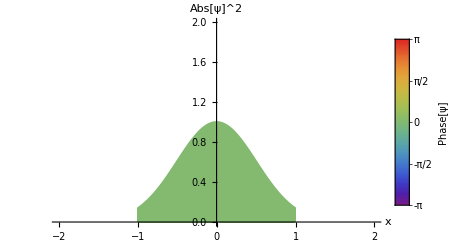

```mathematica
PlotWavefunction[
	Exp[-x^2],
	{x, -1, 1},
	PlotRange -> {{-2, 2}, {0, 2}}
]
```

```mathematica
Options[PlotWavefunction]
```

{Potential→None,PotentialTransform→(#1&),PotentialPlotOptions→{},ShowBar→True,ColorScheme→Rainbow}